```mathematica
<< peeters`;
peeters`setGitDir["../project/figures/ece1505-convex-optimization"]
(*?peeters`exportForLatex*)
```

/Users/pjoot/project/figures/ece1505-convex-optimization

```mathematica
p1 = Plot3D[ x^2 + y^2 , {x,-2,2}, {y,-2,2}, PlotRange -> {Automatic, Automatic,  {0,8}}, AxesLabel-> {"x_1","x_2","F_0(x)"}, Ticks -> None]
peeters`exportForLatex[ "ConvexObjectiveFunctionFig1", p1]
```

-Graphics3D-

{ConvexObjectiveFunctionFig1.eps,ConvexObjectiveFunctionFig1pn.png}

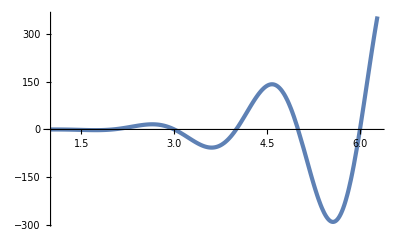

{NonConvexObjectiveFunctionFig2.eps,NonConvexObjectiveFunctionFig2pn.png}

```mathematica
p2 = Plot[ x^3Log[x] Sin[Pi x], {x,1,2 Pi}, Ticks -> None, PlotTheme-> "ThickLines"]
peeters`exportForLatex[ "NonConvexObjectiveFunctionFig2", p2]
```

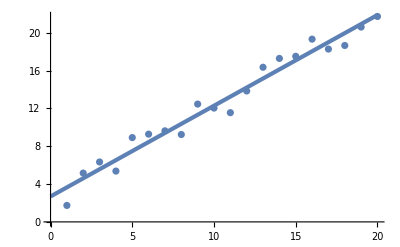

{LinearFitFig3.eps,LinearFitFig3pn.png}

```mathematica
ClearAll[r,rp,lm]
r = {Range[20],RandomReal[5, {20}]} // Transpose ;
rp = {# // First, (# // Last )+ #// First} &/@ r ;
lm[xx_]:=(LinearModelFit[rp,x,x]//Normal) /. x -> xx
p3 = Show[ListPlot[rp, Ticks -> None],Plot[lm[y],{y,0,20}, PlotTheme-> "ThickLines"]]
peeters`exportForLatex[ "LinearFitFig3", p3]
```

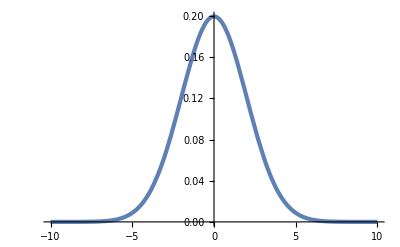

{GaussianFig4.eps,GaussianFig4pn.png}

```mathematica
(*Integrate[Exp[-x^2/8]/Sqrt[ 8 Pi ], {x,-Infinity, Infinity}]*)
p4 = Plot[Exp[-x^2/8]/Sqrt[ 8 Pi ], {x,-10, 10}, Ticks -> None, PlotTheme-> "ThickLines"]
peeters`exportForLatex[ "GaussianFig4", p4]
```

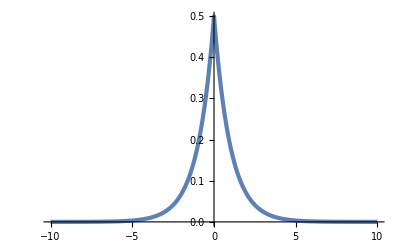

{DoubleSidedExponentialDistFig5.eps,DoubleSidedExponentialDistFig5pn.png}

```mathematica
pde[z_,c_] := (1/2/c) Exp[ -Abs[z]/c] ;
(*Integrate[pde[z,1], {z,-Infinity, Infinity}]*)
p5 = Plot[pde[x,1], {x,-10, 10}, Ticks -> None, PlotTheme-> "ThickLines", PlotRange-> Full]
peeters`exportForLatex[ "DoubleSidedExponentialDistFig5", p5]
```

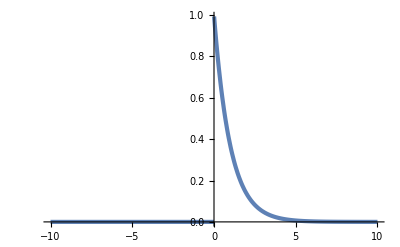

{SingleSidedExponentialDistFig6.eps,SingleSidedExponentialDistFig6pn.png}

```mathematica
pdes[z_,c_] := (1/c) HeavisideTheta[z]Exp[ -Abs[z]/c] ;
(*Integrate[pdes[z,1], {z,0, Infinity}]*)
p6 = Plot[pdes[x,1], {x,-10, 10}, Ticks -> None, PlotTheme-> "ThickLines", PlotRange-> Full]
peeters`exportForLatex[ "SingleSidedExponentialDistFig6", p6]
```

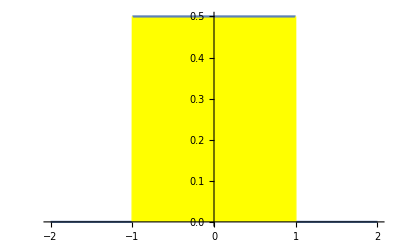

{stepProbabilityDistFig7.eps,stepProbabilityDistFig7pn.png}

```mathematica
step[x_, c_] := (1/2/c) (-UnitStep[x - c]+UnitStep[x+c]);
p7 = Plot[step[x,1], {x,-2,2}, Filling->Axis,FillingStyle->Yellow, Ticks->None]
peeters`exportForLatex[ "stepProbabilityDistFig7", p7]
```